```mathematica
pHard[fid_,n_]:=fid^(2n)
inFid[outFid_,n_]:=outFid^(1/(2n))
```

-Graphics3D-

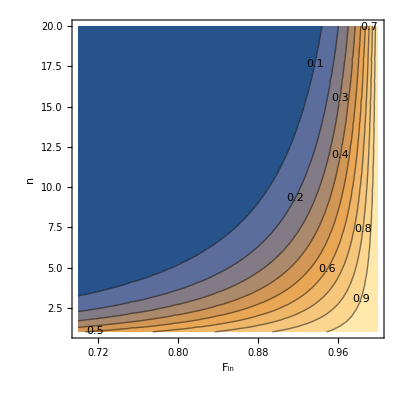

```mathematica
Plot3D[pHard[fid,n],{fid,0,1},{n,1,20},PlotRange->{0,1},BaseStyle->{FontSize->14},AxesLabel->{"F_in","n","  F_out"}]

ContourPlot[pHard[fid,n],{fid,0.7,1},{n,1,20},PlotRange->{0,1},ContourLabels->True,FrameLabel->{"F_in","n","F_out"},BaseStyle->{FontSize->14}]
```

```mathematica
inFid[0.9,10]
inFid[0.9,20]
inFid[0.9,30]
```

0.994746

0.997369

0.998246

```mathematica
inFid[0.8,10]
inFid[0.8,20]
inFid[0.8,30]
```

0.988905

0.994437

0.996288

```mathematica
inFid[0.7,10]
inFid[0.7,20]
inFid[0.7,30]
```

0.982324

0.991123

0.994073